# The Bart - Gohberg - Kaashoek - Van Dooren Theorem

### Load NCGB

```mathematica
<<NC`
<<NCAlgebra`
<<NCGBX`
<<NCPolyGroebner`
```

You are using the version of NCAlgebra which is found in:

/Users/mauricio/NC/

You can now use "<< NCAlgebra`" to load NCAlgebra.

## Step 1

```mathematica
Clear[A,B,C,m1,m2,n1,n2,a,b,c,e,f,g]
SetNonCommutative[A,B,C,m1,m2,n1,n2,a,b,c,e,f,g];
```

Clear::wrsym: Symbol C is Protected.

SetNonCommutative::Protected: WARNING: Symbol C is protected. You should seriously consider not setting it as noncommutative.

```mathematica
FAC={A**m1-m1**a-m2**f**c,A**m2-m2**e,B-m1**b-m2**f,-c+C**m1,-g+C**m2,n1**m1-1,n1**m2,n2**m1,n2**m2-1,m1**n1+m2**n2-1};
```

```mathematica
Length[FAC]
```

10

```mathematica
SetKnowns[A,B,C];
SetUnknowns[m1,m2,n1,n2,a,b,c,e,f,g];
```

```mathematica
FACans1=NCProcess[FAC,2, MaxDigest->2, InfiniteDigest->True,VerboseLevel->1,RemoveRedundant->True];
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: A<B<C≪ m1≪ m2≪ n1≪ n2≪ a≪ b≪ c≪ e≪ f≪ g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 14 polys in the basis, 17 obstructions

> MAJOR Iteration 2, 19 polys in the basis, 34 obstructions

* Removing redundant polynomials

* Basis reduced to 10 polynomials

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 10 polynomials

* * * * * * * * * * * * * * * *

* * * * * * * * * * * * * * * *

*      NCProcess  Report      *

* * * * * * * * * * * * * * * *

> Current order:

A<B<C≪ m1≪ m2≪ n1≪ n2≪ a≪ b≪ c≪ e≪ f≪ g

> The following variables have been solved for:

1. | c→C**m1
2. | g→C**m2
3. | e→n2**A**m2
4. | f→n2**B-n2**m1**b

> The following variables have not been solved for:

,,aAbBCm1m2n1n2

> The following relations involve 2 unknowns:

+ in unknowns {m1,n1}:

1. | n1**m1→1

+ in unknowns {m1,n2}:

1. | n2**m1→0

+ in unknowns {m2,n1}:

1. | n1**m2→0
2. | n1**A**m2→0

+ in unknowns {m2,n2}:

1. | n2**m2→1

> The following relations involve more than 2 unknowns:

+ in unknowns {m1,m2,n1,n2}:

1. | m2**n2→1-m1**n1

```mathematica
FACans1
```

<|Solved→{c→C**m1,g→C**m2,b→n1**B,e→n2**A**m2,f→n2**B-n2**m1**b},0→<||>,1→<||>,2→<|{m1,n1}→{n1**m1→1,m1**n1**B**C**m1→-A**m1+B**C**m1+m1**n1**A**m1},{m1,n2}→{n2**m1→0},{m2,n1}→{n1**m2→0,n1**A**m2→0},{m2,n2}→{n2**m2→1}|>,∞→<|{m1,m2,n1,n2}→{m2**n2→1-m1**n1}|>|>

## Step 2

```mathematica
Clear[P1]
```

```mathematica
SetNonCommutative[P1];
```

```mathematica
SetKnowns[P1,A,B,C];
SetUnknowns[{m1,m2,n1,n2},{a,b,c,e,f,g}];
```

```mathematica
discovered={m1**n1-P1,n1**m1-1,n2**m2-1,m2**n2-1+m1**n1};
(*relations=Union[FACans1[[2]],FACans1[[3]],discovered];*)
```

```mathematica
discovered={m1**n1-P1}
relations=Union[FAC,discovered]
```

{-P1+m1**n1}

{-c+C**m1,-g+C**m2,-P1+m1**n1,A**m2-m2**e,B-m1**b-m2**f,-1+m1**n1+m2**n2,-1+n1**m1,n1**m2,n2**m1,-1+n2**m2,A**m1-m1**a-m2**f**c}

```mathematica
Length[relations]
```

11

```mathematica
FACans2=NCProcess[relations,3,VerboseLevel->1,RemoveRedundant->True,CleanUpBasis->True];
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: P1<A<B<C≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 18 polys in the basis, 16 obstructions

> MAJOR Iteration 2, 22 polys in the basis, 26 obstructions

> MAJOR Iteration 3, 28 polys in the basis, 48 obstructions

* Cleaning up...

* Removing redundant polynomials

* Basis reduced to 11 polynomials

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 11 polynomials

* * * * * * * * * * * * * * * *

* * * * * * * * * * * * * * * *

*      NCProcess  Report      *

* * * * * * * * * * * * * * * *

> Current order:

P1<A<B<C≪ m1<m2<n1<n2≪ a<b<c<e<f<g

> The following variables have been solved for:

1. | c→C**m1
2. | g→C**m2
3. | e→n2**A**m2
4. | a→n1**A**m1-n1**B**C**m1+n1**m1**n1**B**C**m1

> The following variables have not been solved for:

,,AbBCfm1m2n1n2P1

> The following relations do not involve any unknowns:

1. | P1**A**A**P1→P1**A**P1**A

> The following relations involve 2 unknowns:

+ in unknowns {m1,n1}:

1. | m1**n1→P1
2. | n1**m1→1

+ in unknowns {m1,n2}:

1. | n2**m1→0

+ in unknowns {m2,n1}:

1. | n1**m2→0

+ in unknowns {m2,n2}:

1. | n2**m2→1

> The following relations involve more than 2 unknowns:

+ in unknowns {m1,m2,n1,n2}:

1. | m2**n2→1-m1**n1

```mathematica
FACans2
```

<|Solved→{c→C**m1,g→C**m2,e→n2**A**m2,a→n1**A**m1-n1**B**C**m1+n1**m1**n1**B**C**m1},0→<|{}→{P1**A**A**P1→P1**A**P1**A}|>,1→<||>,2→<|{m1,n1}→{m1**n1→P1,n1**m1→1},{m1,n2}→{n2**m1→0},{m2,n1}→{n1**m2→0},{m2,n2}→{n2**m2→1}|>,∞→<|{m1,m2,n1,n2}→{m2**n2→1-m1**n1}|>|>

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: P1<A<B<C≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 18 polys in the basis, 16 obstructions

> MAJOR Iteration 2, 22 polys in the basis, 26 obstructions

> MAJOR Iteration 3, 28 polys in the basis, 48 obstructions

* Cleaning up...

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 28 polynomials

* * * * * * * * * * * * * * * *

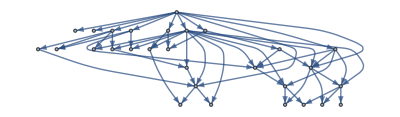
{{c→C**m1,g→C**m2,m1**n1→P1,m2**n2→1-m1**n1,n1**m1→1,n1**m2→0,n2**m1→0,n2**m2→1,n1**P1→n1,P1**m1→m1,P1**m2→0,n1**A**m2→0,b→n1**B,n2**P1→0,e→n2**A**m2,P1**A**m2→0,f→n2**B,P1**P1→P1,n1**A**P1→n1**A,a→n1**A**m1-n1**B**C**m1+n1**m1**n1**B**C**m1,P1**B**C**m1→-A**m1+B**C**m1+P1**A**m1,P1**A**P1→P1**A,n1**A**A**m2→0,P1**B**C**P1→-A**P1+B**C**P1+P1**A**P1,n2**B**C**m1→n2**A**m1-n2**P1**A**m1,P1**A**A**m2→0,n1**A**A**P1→n1**A**P1**A,P1**A**A**P1→P1**A**P1**A},-Graphics-}

```mathematica
{gg1,graph}=NCMakeGB[relations,3,VerboseLevel->1,ReturnGraph->True,RemoveRedundant->False,CleanUpBasis->True]
```

```mathematica
Pick[VertexList[graph],VertexInDegree[graph],_?(#≤1&)]
```

{0,1,2,3,4,5,6,7,8,15,20,28}

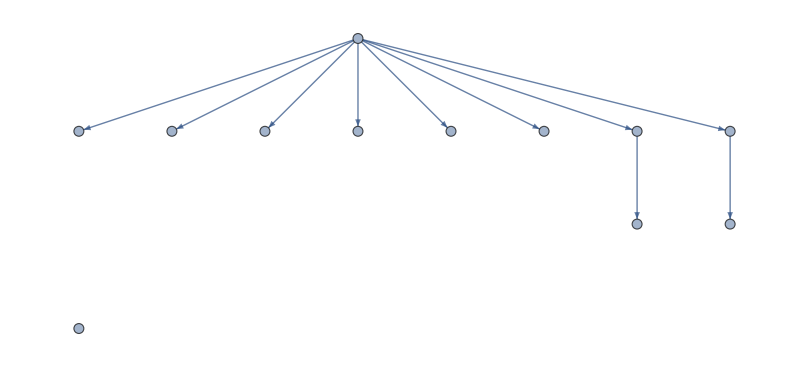

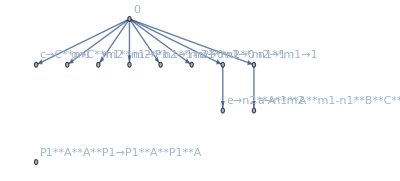

```mathematica
Subgraph[graph,Pick[VertexList[graph],VertexInDegree[graph],_?(#≤1&)]]
VertexReplace[%,Thread[Range[Length[gg1]]->gg1]];
Graph[%,VertexLabels->"Name"]
```

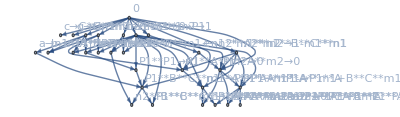

```mathematica
VertexReplace[graph,Thread[Range[Length[gg1]]->gg1]];
Graph[%,VertexLabels->"Name"]
```

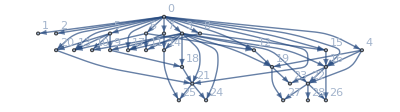

```mathematica
Graph[graph,VertexLabels->"Name"]
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: A<B<C≪ P1≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 18 polys in the basis, 16 obstructions

> MAJOR Iteration 2, 22 polys in the basis, 26 obstructions

* Removing redundant polynomials

* Basis reduced to 15 polynomials

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 15 polynomials

* * * * * * * * * * * * * * * *

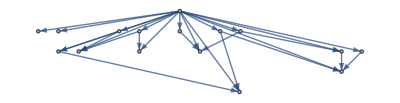
{{P1**A**m2→0,P1**B**C**m1→-A**m1+B**C**m1+P1**A**m1,m1**n1→P1,m2**n2→1-P1,n1**m1→1,n1**m2→0,n2**m1→0,n2**m2→1,n1**A**m2→0,a→n1**P1**A**m1,b→n1**B,c→C**m1,e→n2**A**m2,f→n2**B,g→C**m2},-Graphics-}

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: A<B<C≪ P1≪ m1<m2<n1<n2≪ a<b<c<e<f<g

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 22 polys in the basis, 35 obstructions

> MAJOR Iteration 2, 31 polys in the basis, 88 obstructions

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 31 polynomials

* * * * * * * * * * * * * * * *

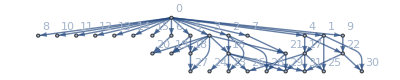
{{P1**P1→P1,P1**A**P1→P1**A,P1**A**A**P1→P1**A**A,P1**B**C**P1→-A**P1+P1**A+B**C**P1,P1**B**C**B**C**P1→A**A**P1-P1**A**A-A**B**C**P1-B**C**A**P1+B**C**B**C**P1+P1**A**B**C**P1+P1**B**C**A**P1,P1**m1→m1,P1**m2→0,n1**P1→n1,n2**P1→0,P1**A**m2→0,n1**A**P1→n1**A,P1**A**A**m2→0,P1**B**C**m1→-A**m1+B**C**m1+P1**A**m1,n1**A**A**P1→n1**A**A,n2**B**C**P1→n2**A**P1,P1**B**C**B**C**m1→A**A**m1-A**B**C**m1-B**C**A**m1-P1**A**A**m1+B**C**B**C**m1+P1**A**B**C**m1+P1**B**C**A**m1,m1**n1→P1,m2**n2→1-P1,n1**m1→1,n1**m2→0,n2**m1→0,n2**m2→1,n1**A**m2→0,n1**A**A**m2→0,n2**B**C**m1→n2**A**m1,a→n1**A**m1,b→n1**B,c→C**m1,e→n2**A**m2,f→n2**B,g→C**m2},-Graphics-}

{}

```mathematica
{gg2,graph}=NCMakeGB[relations,2,VerboseLevel->1,ReturnGraph->True,RemoveRedundant->True]
{gg3,graph}=NCMakeGB[gg2,2,VerboseLevel->1,ReturnGraph->True,RemoveRedundant->False]
Complement[gg1,gg3]
```